# Minimal Integrity Bases for Invariant Algebras and Covariant Modules of Finite Dimensional SO(3)-Representations

Michael Liu

## Abstract

We provide an algorithm that enumerates minimal integrity bases for the set of SO(3)-equivariant polynomials between finite dimensional SO(3)-representations in time polynomial in TODO and space polynomial in TODO.

Our approach is to explicitly compute the isotypic decomposition of the symmetric power of a finite dimensional SO(3)-representation using Schur-Weyl duality and Clebsch-Gordan theory. We then extract generators degree by degree using Nakayama’s lemma.

We apply our algorithm to TODO

## Introduction

#### Contributions

Let G:=SO(3), let X and Y be finite dimensional G-representations, let M:=(𝒮(X^*)⊗Y)^G be the covariant module of G-equivariant polynomials from X to Y, and let R:=(𝒮(X^*))^G be the invariant algebra of G-invariant polynomials on X. Let H_λ be the SO(3) irrep with label λ∈Λ:=, and let X≅⊕_(λ∈Λ)H_λ⊗Hom_G(H_λ,X) and Y≅⊕_(λ∈Λ)H_λ⊗Hom_G(H_λ,Y) be the isotypic decompositions of X and Y.

We provide an algorithm to enumerate a vector space basis for M in time O(blah) and space O(blah) (Algorithm 1). We then use Nakayama’s Lemma to enumerate

a minimal generating set for M as an R-module in time O(blah) and space O(blah) (Algorithm 2), as well as

a minimal generating set for R as an ℝ-algebra in time O(blah) and space O(blah) (Algorithm 3).

#### Relationship to previous work

Algorithm | X | Y | Time | Space | Method
Ours | arbitrary representation | arbitrary irrep | O() | O() | isotypic decomposition,Nakayama
□ | □ | □ | □ | □ | Gordon
□ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □

#### Applications

Constitutive modeling

## Overview

Write M≅⊕_(D∈)M^D and R≅⊕_(D∈)R^D, where M^D:=(𝒮^D(X^*)⊗Y)^G is the set of degree D homogeneous G-equivariant polynomials from X to Y, and R^D:=(𝒮^D(X^*))^G is the set of degree D homogeneous G-invariant polynomials on X. Now, suppose that Y=H_ν. Then M^D=(𝒮^D(X^*)⊗H_ν)^G≅Hom_G(H_ν,𝒮^D(X^*)), which is precisely the multiplicity space corresponding to H_ν in the isotypic decomposition of 𝒮^D(X^*)≅⊕_(ν∈Λ)H_ν⊗Hom_G(H_ν,𝒮^D(X^*)). Similarly, R^D≅Hom_G(H_0,𝒮^D(X^*)) is precisely the multiplicity space corresponding to H_0 in the isotypic decomposition of 𝒮^D(X^*). Therefore, our first goal is to explicitly determine the isotypic decomposition of 𝒮^D(X^*).

#### Theorem 1 (Isotypic decomposition of 𝒮^D(X^*))

Write X_λ:=Hom_G(H_λ,X) for convenience. There exists a G-equivariant isomorphism

𝒮^D(X^*)≅⊕_(ν∈Λ)H_ν⊗(⊕_((d_λ)_λ)⊕_((π_λ)_λ)⊕_((μ_λ)_λ)Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))))⊗(⊗_λ e_π_λ^*(X_λ^(⊗d_λ)))),

where

λ ranges over all nonnegative integers such that X_λ!=0,

(d_λ)_λ ranges over all sequences of nonnegative integers such that ∑_λ d_λ=D,

(π_λ)_λ ranges over all sequences of integer partitions π_λ⊢d_λ such that each partition has largest part at most min(dim H_λ,dim X_λ), and

(μ_λ)_λ ranges over all sequences of nonnegative integers such that all Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))) are nonzero and Hom_G(H_ν,⊗_λ H_μ_λ) is nonzero.

#### Proof

See Appendix A.

#### Remark

In Eq. (1), the nested direct sums over (d_λ)_λ, (π_λ)_λ, and (μ_λ)_λ are naturally represented with a tree structure. At each leaf of this tree structure, the spaces Hom_G(H_ν,⊗_λ H_μ_λ), Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))), and e_π_λ^*(X_λ^(⊗d_λ)) are most efficiently represented with corresponding vector space bases. Thus, for any given D and ν, we obtain a representation of the multiplicity space Hom_G(H_ν,𝒮^D(X^*)) as an isotypic data tree (see Example 1).

#### Remark

By enumerating a basis for the right-hand-side of Eq. (1) and passing this basis through the isomorphism in Eq. (1), we obtain a basis for 𝒮^D(X^*) that corresponds to the isotypic decomposition of 𝒮^D(X^*). In particular, we may use the angular momentum basis for H_ν, the Clebsch-Gordan tensor basis for Hom_G(H_ν,⊗_λ H_μ_λ), and the SSYT basis for e_π_λ^*(X_λ^(⊗d_λ)). The only space for which a basis is not currently on hand is Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))). Thus, we describe how to obtain such a basis using Clebsch-Gordan tensor trees.

#### Theorem 2 (Isotypic decomposition of e_π_λ(H_λ^(⊗d_λ)))

There exists a G-equivariant isomorphism

e_π_λ(H_λ^(⊗d_λ))≅⊕_μ_λ H_μ_λ⊗r_π_λ(⊕_((ξ_(λ,p))_p)Hom_G(H_μ_λ,⊗_p H_(ξ_(λ,p)))⊗(⊗_p Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ)))),

where (ξ_(λ,p))_p ranges over all sequences of nonnegative integers such that all Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ)) are nonzero and Hom_G(H_μ_λ,⊗_p H_(ξ_(λ,p))) is nonzero.

#### Proof

See Appendix B.

#### Remark

An elementary tensor in

Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))))⊗(⊗_λ e_π_λ^*(X_λ^(⊗d_λ)))

can be viewed as a tensor tree along with a SSYT. We say that p∈S^D(X) corresponds to the isotypic data in the spaces Hom_G(H_ν,⊗_λ H_μ_λ), Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))), and e_π_λ^*(X_λ^(⊗d_λ)) if p is the image of this data under the isomorphism in Eq. (1).

#### Theorem 3 (Evaluation scheme)

Let p∈𝒮^D(X^*) be specified by its isotypic data, i.e., a choice of C∈Hom_G(H_ν,⊗_λ H_μ_λ), L_λ∈Hom_G(H_μ_λ,H_λ^(⊗d_λ)), and T_λ∈X_λ^(⊗d_λ). Moreover, write x∈X as

x=⊕_λ x_λ,

where each x_λ∈H_λ⊗X_λ is further written as

x_λ=⊕_k_λ h_(λ k_λ)⊗m_(λ k_λ)

for some h_(λ k_λ)∈H_λ, and some fixed orthonormal basis {m_(λ k_λ)}_(k_λ=1)^(dim X_λ) for X_λ. Then p(x) can be evaluated by contracting the tensor tree with the SSYT monomial,

p(x)=(D
(d_λ)_λ)C·⊗_λ(r_π L_λ·c_πf(T_λ)),

where f maps m_(λ k_λ) to h_(λ k_λ).

#### Proof

See Appendix C.

#### Example 1 (Basis for ⊕_(D=0)^3 Hom_G(H_0,𝒮^D(H_1⊕H_1⊕H_2)))

Suppose we wish to enumerate a basis for the space of G-invariant polynomials of degree at most 3 acting on two vectors and one harmonic tensor as inputs. In our setting, this corresponds to the data X=(H_1⊗ℂ^2)⊕(H_2⊗ℂ^1), Y=H_0, and D=3. We represent this data as follows.

```mathematica
λs={1,2};
mλs={2,1};
ν=0;
DMax=3;
```

The isotypic data tree representing ⊕_(D=0)^3 Hom_G(H_0,𝒮^D(X^*)) according to Eq. (1) is then

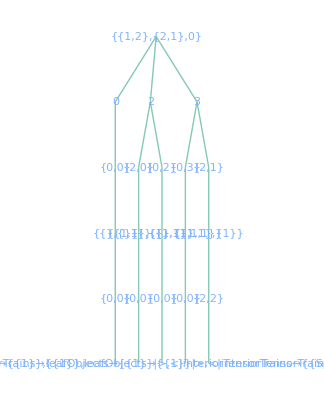

```mathematica
tree=IsotypicDataTree[λs,mλs,ν,DMax]
```

The isotypic data tree stores the following information:

Level | Symbol | Meaning
0 | {(λ)_λ,(dim X_λ)_λ,ν} | X=⊕_λ H_λ⊗X_λ and Y=H_ν
1 | D | total polynomial degree
2 | (d_λ)_λ | multidegree in the H_λ
3 | (π_λ)_λ | partitions determining the partial symmetry of tensors
4 | (μ_λ)_λ | intermediate spins coupled to H_ν
5 | <|…|> | bases forHom_G(H_ν,⊗_λ H_μ_λ),Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))),and e_π_λ^*(X_λ^(⊗d_λ))

Next, we contract the tensor tree with the Young-symmetrized SSYT monomial in the input tensors to obtain an equivariant polynomial. This produces a basis for Hom_G(H_0,𝒮^3(H_1⊕H_2)).

```mathematica
polys=Chop@FullSimplify@Flatten@SphericalBasisToMonomialBasis@EvaluateVectorSpaceBases[alg,generateVariables[λs,mλs]];
```

## Algorithms

#### Algorithm (IsotypicDataTree)

Inputs: (λ∈Λ)_λ, (m_λ∈ℕ)_λ, ν∈Λ, D_max∈ℕ
Output: IsotypicDataTree

store {λs,mλs,ν} at the root of a tree

for each D∈{∑_λ m_λ,...,D_max}

spawn a new leaf containing D

for each leaf D

for each (d_λ∈ℕ)_λ with ∑_λ d_λ=D

spawn a new leaf containing (d_λ)_λ

for each leaf (d_λ)_λ

for each (π_λ⊢d_λ)_λ with each π_(λ,1)<=min{dim H_λ,dim M_λ}

spawn a new leaf containing (π_λ)_λ

for each leaf (π_λ)_λ

for each (μ_λ∈Λ)_λ with each H_μ_λ appearing in e_π_λ(H_λ^(⊗d_λ)) and H_ν appearing in ⊗_λ H_μ_λ

spawn a new leaf containing (μ_λ)_λ

for each path from root to leaf

compute a basis for Hom_G(H_ν,⊗_λ H_μ_λ)

compute a basis for each Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))

enumerate all SSYT with shapes (π_λ)_λ filled with entries from {1,...,dim X_λ}

```mathematica
KroneckerProduct[{a,b,c},{d,e,f}]
```

{{a d,a e,a f},{b d,b e,b f},{c d,c e,c f}}

```mathematica
KroneckerProduct[{{a},{b},{c}},{{d,x},{e,y},{f,z}}]
```

{{a d,a x},{a e,a y},{a f,a z},{b d,b x},{b e,b y},{b f,b z},{c d,c x},{c e,c y},{c f,c z}}

#### Lemma

IsotypicDataTree has operation count

#### Algorithm (Evaluation scheme)

#### Theorem 4 (Evaluation scheme, continued)

From [TODO], we have

Sym(h_1^(⊗d_1)⊗…⊗h_m^(⊗d_m))=1/C∑_(0<=a_i<=d_i) (h_1+ζ_2^a_2 h_2...+ζ_m^a_m h_m)^d ζ_2^a_2... ζ_m^a_m,
C:=(d
d_1,...,d_m)(d_1+1)...(d_m+1).

Thus,

## Algebra Basis for the Invariant Ring

#### Random Sampling

Explain the random sampling part rigorously! This will help you understand the code better.

#### Lemma (Nakayama)

Let M=⊕_(D∈ℕ_0)M_D be a finitely generated graded module over a graded ring R=⊕_(D∈ℕ_0)R_D, where R_0=ℝ. Let I:=⊕_(D∈ℕ)R_D be the ideal generated by the positively graded elements of R. Let L⊆M. Then L/I M is a basis for M/I M as an ℝ-vector space iff L is a minimal generating set for M as an R-module.

#### Remark

Suppose that we are given vector space bases ℛ_D,ℳ_D for R_D,M_D. Note that

I M=⊕_(D∈ℕ)(I M)_D,

where

(I M)_D:=I M∩M_D=∑_(1<=D'<=D) R_D' M_(D-D')=Span{r_D' m_(D-D')|1<=D'<=D,r_D'∈ℛ_D',m_(D-D')∈ℳ_(D-D')}.

Since

M/I M≅⊕_(D∈ℕ)M_D/(I M)_D,

we can proceed degree-by-degree to obtain a vector space basis for N/I N. Define

D_max:=max{D∈ℕ|M_D/(I M)_D!=0},

which may be difficult to determine in practice.

For each 1<=D<=D_max, compute a basis for (I M)_D and extend it to a basis for M_D by adjoining the basis vectors in the set L_D⊆M_D. Write L:=∪_(D∈ℕ)L_D. Since L_D/(I M)_D is a basis for M_D/(I M)_D, L/I M is a basis for M/I M, so by Nakayama’s Lemma, L is a minimal generating set for M as an R-module.

Next, apply the above algorithm with N=I. Let ℝ[L] be the ℝ-algebra generated by L. Clearly, ℝ⊆ℝ[L]. Now, write R_(<=D):=R_0⊕…⊕R_D, and suppose that R_(<=D)⊆ℝ[L]. Then

R_(D+1)=I_(D+1)⊆Span_ℝ(L_(D+1))+(I^2)_(D+1)=Span_ℝ(L_(D+1))+∑_(1<=D'<=D) I_D' I_(D+1-D').

Clearly, Span_ℝ(L_(D+1))⊆ℝ[L], and by the inductive hypothesis, I_1,...,I_D⊆R_(<=D)⊆ℝ[L]. Thus, R=ℝ[L]. To see that L is minimal, note that if any L⊆I generates R as an ℝ-algebra, then L generates I as an R-module, so L/I^2 generates I/I^2 as an ℝ-module. Thus, since our given L makes L/I^2 a basis for I/I^2, our given L is a minimal generating set for R as an ℝ-algebra.

### Algorithms

Given D_max∈ℕ and ℛ_D,𝒩_D for all D=0,1,2,...,D_max,

For D=1,2,...,D_max

compute a spanning set for (I M)_D using Eq. (TODO)

extend the above to a basis for M_D by evaluating the new basis vectors in ℳ_D at the same random points and finding pivot columns L_D

#### Compute a spanning set for (I M)_D

For D'=1,2,...,D

For r_D'∈ℛ_D',m_(D-D')∈𝒩_(D-D')

evaluate r_D' and m_(D-D') at random points and Outer

## Appendix: Preliminaries (honestly, this is more like algorithm stuff)

#### Definition (Elementary Clebsch-Gordan tensor)

For any λ:=(λ_1,λ_2),γ:=(γ_1,γ_2)∈Λ^2 such that λ_1=γ_1 and |λ_1-λ_2|<=γ_2<=λ_1+λ_2, the elementary Clebsch-Gordan tensor CG(λ,γ) is the unique element in (H_λ_1⊗H_λ_2⊗H_γ_2)^G normalized via the Condon–Shortley phase convention.

#### Definition (Iterated Clebsch-Gordan tensor)

For any λ:=(λ_1,…,λ_d),γ:=(γ_1,…,γ_d)∈Λ^d such that λ_1=γ_1 and |λ_j-λ_(j+1)|<=γ_(j+1)<=λ_j+λ_(j+1) for all 1<=j<=d-1, the Clebsch-Gordan tensor CG(λ,γ) is the unique element in (H_λ_1⊗…⊗H_λ_d⊗H_γ_d)^G with the tensor train factorization

CG(λ,γ):=∏_(j=1)^(d-1) CG((γ_j,λ_(j+1)),(γ_j,γ_(j+1))),

where the product denotes tensor contraction.

#### Theorem (Isotypic decomposition of the tensor product of two G-irreps)

Let H_λ_1,H_λ_2 be G-irreps. Then

H_λ_1⊗H_λ_2≅⊕_(γ_2=|λ_1-λ_2|)^(λ_1+λ_2)H_γ_2⊗Hom_G(H_γ_2,H_λ_1⊗H_λ_2).

Moreover, a basis for Hom_G(H_γ_2,H_λ_1⊗H_λ_2) is given by the single Clebsch-Gordan tensor CG(λ,γ), where λ:=(λ_1,λ_2) and γ:=(λ_1,γ_2).

#### Theorem (Isotypic decomposition of the tensor product of multiple G-irreps)

Let H_λ_1,...,H_λ_d be G-irreps. Then

H_λ_1⊗…⊗H_λ_d≅⊕_(μ=Max[0,2m-s])^s H_μ⊗Hom_G(H_μ,H_λ_1⊗…⊗H_λ_d),

where s:=λ_1+…+λ_d and m:=Max[λ_1,…,λ_d]. Moreover, a basis for Hom_G(H_μ,H_λ_1⊗…⊗H_λ_d) is given by the Clebsch-Gordan tensors CG(λ,γ), where λ:=(λ_1,…,λ_d), and γ ranges over all γ:=(γ_1,…,γ_d)∈Λ^d such that |λ_j-λ_(j+1)|<=γ_(j+1)<=λ_j+λ_(j+1) and γ_d=μ.

#### Remark

The coordinates of the Clebsch-Gordan tensor in the angular momentum basis are well known. For any λ_1,λ_2,λ_3∈Λ and any m_1,m_2,m_3∈ℤ, denote by

(λ_1 | λ_2 | λ_3
m_1 | m_2 | m_3)∈ℝ

the corresponding Clebsch-Gordan coefficient, which can be computed using the ClebschGordan function in Mathematica. Note that the Clebsch-Gordan coefficient is nonzero iff |λ_1-λ_2|<=λ_3<=λ_1+λ_2, |m_j|<=λ_j for all j, and m_3=m_1+m_2. Then for any valid λ,γ∈Λ^d, we have in coordinates

CG(λ,γ)=∏_(j=1)^(d-1) (γ_j | λ_(j+1) | γ_(j+1)
s_j | m_(j+1) | s_(j+1))∈ℝ^(2 λ_1+1)⊗…⊗ℝ^(2 λ_d+1)⊗ℝ^(2 γ_d+1),

where s_j:=m_1+…+m_j, and the free indices are m_1,…,m_d along with the last index s_d, which is completely determined by the m_j. Note that the Clebsch-Gordan tensor CG(λ,γ) is nonzero iff |γ_j-γ_(j+1)|<=λ_(j+1)<=γ_j+γ_(j+1) for all 1<=j<=d-1 and |m_j|<=λ_j ,|s_j|<=γ_j for all 1<=j<=d. Moreover, it is always the case that (1,2)CG(λ,γ)=(-1)^γ_2 CG(λ,γ).

#### Remark

In our setting, Schur-Weyl duality provides a clean way to bookkeep irrep multiplicity in the input space X.

#### Definition (Young symmetrizer)

Let π be an integer partition of d∈ℕ, and let T_π be the associated standard Young tableau filled in English-reading order. Define

R_π:={σ∈𝔖_d|σ preserves every row of T_π},
C_π:={σ∈𝔖_d|σ preserves every column of T_π}.

The row antisymmetrizer, column symmetrizer, and Young symmetrizer are, respectively,

r_π:=1/(|R_π|)∑_(σ∈R_π) sgn(σ)σ,
c_π:=1/(|C_π|)∑_(σ∈C_π) σ,
e_π:=(|R_π||C_π|)/HL_π c_π r_π,

where HL_π is the hook length product of π.

#### Lemma (Basis for e_π(V^(⊗d)))

Let V be a vector space with basis {v_1,…,v_n}. Then e_π(V^(⊗d)) has a basis

{e_π(T)|T ranges over all SSYT monomials of shape π filled with entries from {v_1,…,v_n}}.

#### Theorem (Schur-Weyl duality)

Let V be a finite dimensional vector space, let the general linear group GL(V) act diagonally on V^(⊗d), and let the symmetric group 𝔖_d act via factor permutation on V^(⊗d). Then

V^(⊗d)≅⊕_π e_π(V^(⊗d))⊗[π]≅⊕_π e_π^*(V^(⊗d))⊗[π]^*,

where the sum is over all integer partitions π of d with largest part at most dim V, and [π] is the Specht module associated with π.

#### Corollary (Cauchy decomposition (Corollary 2.3.3 in [W03]))

Let V,W be finite dimensional. Then

𝒮^d(V⊗W)≅⊕_π e_π(V^(⊗d))⊗e_π^*(W^(⊗d)),

where the sum is over all integer partitions π of d with largest part at most min(dim V,dim W).

#### Proof

𝒮^d(V⊗W)=((V⊗W)^(⊗d))^(𝔖^d)
≅(V^(⊗d)⊗W^(⊗d))^(𝔖^d)
≅^(Schur-Weyl)((⊕_(π⊢d,π_1<=dim V)e_π(V^(⊗d))⊗[π])⊗(⊕_(π⊢d,π_1<=dim W)e_π^*(W^(⊗d))⊗[π]^*))^(𝔖^d)
≅^(Schur Lemma)⊕_(π⊢d,π_1<=min{dim V,dim W})e_π(V^(⊗d))⊗e_π^*(W^(⊗d)),

## Appendix A: Proof of Theorem 1

We have

𝒮^D(X^*)=𝒮^D(⊕_λ H_λ⊗X_λ)
≅^Sym⊕_((d_λ)_λ)⊗_λ 𝒮^d_λ(H_λ⊗X_λ)
≅^(rearrange ⊗, Sym)⊕_((d_λ)_λ)⊗_λ⊕_π_λ e_π_λ(H_λ^(⊗d_λ))⊗e_π_λ^*(X_λ^(⊗d_λ))
≅^(rearrange ⊗)⊕_((d_λ)_λ)⊕_((π_λ)_λ)(⊗_λ e_π_λ(H_λ^(⊗d_λ)))⊗(⊗_λ e_π_λ^*(X_λ^(⊗d_λ))),

where the third line is due to the Cauchy decomposition. Since each intermediate isomorphism is unitary and G-equivariant, so is the composition.

We have

⊗_λ e_π_λ(H_λ^(⊗d_λ))≅^(apply Hom)⊗_λ⊕_μ_λ H_μ_λ⊗Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))≅^(rearrange ⊗)⊕_((μ_λ)_λ)(⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))).

Clebsch-Gordan yields

⊗_λ H_μ_λ≅^(apply Hom)⊕_(ν∈Λ)H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ).

Thus,

⊗_λ e_π_λ(H_λ^(⊗d_λ))≅⊕_(ν∈Λ)⊕_((μ_λ)_λ)H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))).

## Appendix B: Proof of Theorem 2

We have

e_π_λ(H_λ^(⊗d_λ))≅r_π_λ(c_π_λ(H_λ^(⊗d_λ)))
≅r_π_λ(⊗_p Λ^(π_(λ,p))(H_λ))
≅^(apply Hom)r_π_λ(⊗_p⊕_(ξ_(λ,p))H_(ξ_(λ,p))⊗Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ)))
≅^(rearrange ⊗)r_π_λ(⊕_((ξ_(λ,p))_p)(⊗_p H_(ξ_(λ,p)))⊗(⊗_p Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ)))).

Clebsch-Gordan yields

⊗_p H_(ξ_(λ,p))≅^(apply Hom)⊕_μ_λ H_μ_λ⊗Hom_G(H_μ_λ,⊗_p H_(ξ_(λ,p))).

Rearrange the tensor product and use the G-equivariance of r_π_λ to conclude.

## Appendix C: Proof of Theorem 3

Allowing for arbitrary rearrangements of the tensor product, we have

x^(⊗D)=⊕_((d_λ)_λ)(D
(d_λ)_λ)(⊗_λ x_λ^(⊗d_λ))

and

x_λ^(⊗d_λ)=⊕_((k_(λ l))_l)⊗_(l=1)^d_λ h_(λ k_(λ l))⊗⊗_(l=1)^d_λ m_(λ k_(λ l)),

so

x^(⊗D)=⊕_((d_λ)_λ)(D
(d_λ)_λ)(⊗_λ⊕_((k_(λ l))_l)⊗_(l=1)^d_λ h_(λ k_(λ l))⊗⊗_(l=1)^d_λ m_(λ k_(λ l))).

The polynomial p(x) is evaluated by pairing 𝒮^D(X^*)𝒮^D(X^*), so

p(x)=px^(⊗D)
=(D
(d_λ)_λ)(C·⊗_λ e_π_λ(L_λ))⊗(⊗_λ e_π_λ^*(T_λ))⊗_λ⊕_((k_(λ l))_l)⊗_l h_(λ k_(λ l))⊗⊗_l m_(λ k_(λ l))
=(D
(d_λ)_λ)C·⊗_λ⊕_((k_(λ l))_l)(e_π_λ(L_λ)⊗_l h_(λ k_(λ l))e_π_λ^*(T_λ)⊗_l m_(λ k_(λ l)))
=^Lemma(D
(d_λ)_λ)C·⊗_λ e_π_λ(L_λ)f(T_λ)

#### Lemma

Let L∈H^(⊗d). Let T be a SSYT with shape π⊢d and entries in {1,...,dim M}. Let {U_k}_k be a complete set of SSYT with shape π and entries in {1,...,dim M}. Fix any collection h_1,...,h_(dim M)∈H and any ONB m_1,...,m_(dim M)∈M. For any Young tableaux U, let f(U) (resp. g(U)) be the corresponding elementary tensor in H^(⊗d) (resp. M^(⊗d)) whose l^th component is h_(U(l)) (resp. m_(U(l))). Then

∑_k e_π(L)f(U_k)e_π^*(g(T))g(U_k)=e_π(L)f(T),

where e_π(L)f(U_k) and e_π(L)f(T) are viewed as polynomials in the h_1,...,h_(dim M)∈H.

#### Proof

We have

e_π^*(f(T))=e_π^*(Φ^(⊗d)g(T))=Φ^(⊗d)e_π^*(g(T))=Φ^(⊗d)∑_k g(U_k)e_π^*(g(T))g(U_k)=∑_k f(U_k)e_π^*(g(T))g(U_k),

Take inner products with e_π(L) to conclude.

## Appendix (Lemmas)

#### Lemma A1 (Identifying the covariant module with the space of equivariant polynomial functions)

There is an isomorphism of vector spaces

(𝒮(X^*)⊗Y)^G≅{equivariant polynomial functions from X to Y}

#### Proof

Consider the pairing (𝒮(X^*)⊗Y)×X->Y defined on elementary tensors (which correspond to the component functions of the polynomial) by

(φ⊗y,x)↦(φ⊗y)(x):=φ(x)y

and extended linearly to 𝒮(X^*)⊗Y, where φ(x) is defined by writing

φ=⊕_(d=0)^D⊕_(j_1,…,j_d=1)^(dim X^*)φ_(j_1(…j)_d)e_j_1^*⊗…⊗e_j_d^*

in terms of a basis {e_j^*}_(j=1)^(dim X^*) for X^* and declaring that

φ(x):=⊕_(d=0)^D⊕_(j_1,…,j_d=1)^(dim X^*)φ_(j_1(…j)_d)e_j_1^*(x)*…*e_j_d^*(x).

Note that φ(x) is a degree D polynomial in the entries of X selected by the e_j^*.

Fix g∈G, ∑_i φ_i⊗y_i∈𝒮(X^*)⊗Y, and x∈X. Observe that

(∑_i φ_i⊗y_i)(g x)=g((∑_i φ_i⊗y_i)(x))
⟺∑_i φ_i(g x)y_i=g(∑_i φ_i(x)y_i)
⟺∑_i (g^-1 φ_i)(x)y_i=∑_i φ_i(x)g y_i
⟺(∑_i g^-1 φ_i⊗y_i)(x)=(∑_i φ_i⊗g y_i)(x).

Thus, we conclude that the polynomial ∑_i φ_i⊗y_i is equivariant iff g∑_i φ_i⊗y_i=∑_i φ_i⊗y_i for all g∈G iff ∑_i φ_i⊗y_i∈(𝒮(X^*)⊗Y)^G.

#### Lemma (Isotypic decomposition of Λ^d(H_λ))

Let λ,d<=3. Then dim Hom_G(H_μ,Λ^d(H_λ)) is either 0 or 1. Moreover, if d=3 and dim Hom_G(H_μ,Λ^d(H_λ))=1, then {λ,2⌊Abs[λ-μ]/2⌋+1,μ} is a nonzero path.

#### Lemma (Isotypic decomposition of 𝒮^d(H_λ))

Let λ,d<=3. Then dim Hom_G(H_μ,𝒮^d(H_λ)) is either 0 or 1. Moreover, if d=3 and dim Hom_G(H_μ,𝒮^d(H_λ))=1, then {λ,2⌊(Abs[λ-μ]+1)/2⌋,μ} is a nonzero path.

#### Proof

We check the isotypic multiplicities by brute force.

```mathematica
data=Table[IsotypicMultiplicityExteriorPower[λ,d,μ],{λ,0,3},{d,1,2λ+1},{μ,0,Sum[i,{i,λ-d+1,λ}]}];
Grid[data,ItemSize->Full]
```

{1} |  |  |  |  |  | 
{0,1} | {0,1} | {1} |  |  |  | 
{0,0,1} | {0,1,0,1} | {0,1,0,1} | {0,0,1} | {1} |  | 
{0,0,0,1} | {0,1,0,1,0,1} | {1,0,1,1,1,0,1} | {1,0,1,1,1,0,1} | {0,1,0,1,0,1} | {0,0,0,1} | {1}

#### Lemma

Let wt(μ_λ) be the number of SSYT filled from {-λ,...,λ} with total of the boxes μ_λ. The multiplicity of H_μ_λ in the isotypic decomposition of e_π_λ(H_λ^(⊗d_λ)) is wt(μ_λ)-wt(μ_λ+1). In particular, if s_π the Schur polynomial corresponding to π, then wt(μ_λ) is the coefficient of x^μ_λ in s_π(x^-λ,x^(-λ+1),...,x^λ).

#### Lemma (Polarization identity for symmetric tensors) https://math.stackexchange.com/questions/481167/polarization-formula

Let Φ be a tensor. Then

Sym Φv_1⊗…⊗v_d=(-1)^d/(d!)∑_(A⊆{1,…,d}) (-1)^(|A|)ϕ(∑_(a∈A) v_a),
ϕ(v):=Φv^(⊗d).

## Appendix: Future Directions

Do the sequences {dim R_D}_D or {dim M_D}_D appear in OEIS? What kinds of connections can be made?

Would the algorithm work better using the polarization identity in place of the CP decomposition for partially symmetrized monomials?

What precisely is the importance of the SSYT? Can some algebra or module redundancy be detected purely by looking at the spin trees?

In particular, any spin tree with a zero interior node is a product of lower degree invariants and covariants. Can this be utilized to improve our algorithm?

## References

[W03]	https://doi.org/10.1017/CBO9780511546556

https://arxiv.org/abs/2406.01552

https://github.com/MichaelLiu2024/Equivariant-Polynomial-Tensor-Functions

## Old Stuff

```mathematica
SpinListToSpinTree[{λs_List,γs_List}]:=
If[
Depth[λs]>2,
SpinListToSpinTree[{SpinListToSpinTree/@λs,γs}],
Fold[Tree[Last@#2,{#1,First@#2}]&,First[λs],Rest@Transpose[{λs,γs}]]
]
SpinListToSpinTree[γs_List]:=With[{λ=First@γs},If[Length[γs]==1,Tree[λ,{λ}],Fold[Tree[#2,{#1,λ}]&,γs]]]
```

```mathematica
DisplaySpinTrees[assoc_Association]:={assoc,Outer[SpinListToSpinTree@*List,Tuples[assoc[["leafPaths"]]],assoc[["corePaths"]],1]}
```

```mathematica
Quit
```

```mathematica
AppendTo[
$Path,
"C:\\Users\\micha\\OneDrive\\Desktop\\Oden\\Notes\\Equivariant-Polynomial-Tensor-Functions-main\\Equivariant-Polynomial-Tensor-Functions-main"
];
Needs["GrowMultiplicitySpaceTree`"];
Needs["UnitTestTools`"]
```

```mathematica
UnitTest[]
```

{1.,-1.73205,-1.73205,-1.73205,1.49071,1.49071,1.49071,-0.929622,-0.929622,-0.929622,-0.929622,1.82574,1.82574,1.82574,1.82574,1.82574,1.82574,0.+1.82574 ⅈ,0.+1.82574 ⅈ,1.9245,0.+2.58199 ⅈ,0.+2.58199 ⅈ,0.+5.16398 ⅈ,0.+5.16398 ⅈ,0.-1.9245 ⅈ,0.-3.849 ⅈ,0.-1.9245 ⅈ,0.-3.849 ⅈ,-2.58199,-1.13855,-1.13855,-1.13855,-1.13855,-1.13855,-1.13855,-1.13855,-1.13855,-2.2771}